## R52A THB1 Fe3+ pH Titration Data Analysis

## Formatting

```mathematica
SetOptions[ListLinePlot,
Axes->False,
AspectRatio->2/3,
BaseStyle->{FontFamily->"Arial",
FontSize->16,
FontWeight->Normal},
ImageSize-> 350,
Frame-> True,
FrameStyle-> AbsoluteThickness[1],
LabelStyle-> Directive[Black]];
SetOptions[ListPlot,
Axes->False,
AspectRatio->2/3,
BaseStyle->{FontFamily->"Arial",
FontSize->16,
FontWeight->Normal},
ImageSize-> 350,
Frame-> True,
FrameStyle-> AbsoluteThickness[1],
LabelStyle-> Directive[Black],
PlotMarkers->{●,15}];
scale=Graphics[Raster[{Range[100]/100},ColorFunction->(
Blend[{{0,Red},{2/4,Yellow},{3/4, Green},
{1,Blue}},#]&)],AspectRatio->.15]
```

-Graphics-

## Data Import

```mathematica
SetDirectory["F:\\190625_R52A_THB1_Fe3_pH_titration"];
data=Import["190625_R52A_THB1_Fe3_pH_titration_corrected.csv"];
Take[data,8]//TableForm
height=Length[data];
width=Length[Transpose[data]];

(*List of wavelengths*)
wavelength=data[[2;;height,1]];
(*List of pH values*)
pHvals=data[[1,2;;width]];
(*List of absorbance values, per pH value*)
abs={};
For[i=1,i<width,i++,AppendTo[abs,data[[2;;height,i+1]]]]
```

Wavelength (nm) | 3.41 | 3.59 | 3.82 | 3.95 | 4.08 | 4.22 | 4.38 | 4.92 | 5.7 | 6.02 | 6.19 | 6.54 | 6.79 | 7.01 | 7.02 | 7.15 | 7.32 | 7.55 | 7.85 | 8.48 | 8.62 | 8.9 | 9.18 | 9.5 | 9.56 | 10.03 | 10.11 | 10.3 | 10.48 | 10.68 | 10.75 | 11.11 | 11.22 | 11.45 | 11.57 | 11.78 | 11.91 | 12.05 | 12.24 | 12.41 | 12.66
750.063 | 0.00139322 | 0.00136275 | 0.00109436 | 0.000621189 | 0.000879278 | 0.000914534 | 0.000773291 | 0.00103011 | 0.00077654 | 0.000601441 | 0.000681576 | 0.000577424 | 0.000626538 | 0.000493019 | 0.00103657 | 0.000856474 | 0.000562452 | 0.000716516 | 0.000982848 | 0.00044301 | 0.000569309 | 0.0000862227 | 0.00105187 | 0.000507456 | 0.000588704 | 0.000333065 | 0.000382128 | 0.000551964 | 0.000533935 | 0.000712279 | 0.000477828 | 0.000643318 | 0.000609543 | 0.00054979 | 0.000770707 | 0.000931171 | 0.000751555 | 0.000832667 | 0.00117648 | 0.00116942 | 0.00186793
749.499 | 0.00102812 | 0.00127507 | 0.00118608 | 0.000610672 | 0.000600909 | 0.000966935 | 0.000388355 | 0.000825665 | 0.00053074 | 0.000429886 | 0.000176388 | 0.000946663 | 0.000365009 | 0.000580777 | 0.000812933 | 0.000548384 | 0.000920912 | 0.000595586 | 0.000664203 | 0.000490356 | 0.000361534 | 0.000264515 | 0.000521764 | 0.000225006 | 0.000310664 | 0.000349557 | 0.000212286 | -0.0000669736 | 0.000241226 | 0.000238376 | 0.000491637 | 0.000425342 | 0.000399729 | 0.000355455 | 0.000469876 | 0.000735038 | 0.000581518 | 0.00107351 | 0.000646385 | 0.000778856 | 0.0015015
748.935 | 0.00133427 | 0.00131858 | 0.00120551 | 0.00078909 | 0.00120831 | 0.000873952 | 0.000667782 | 0.000770529 | 0.000631827 | 0.000606133 | 0.000841281 | 0.000858653 | 0.000468419 | 0.000623341 | 0.00094278 | 0.000647539 | 0.000936765 | 0.000897223 | 0.000867778 | 0.000573716 | 0.000680082 | 0.000426013 | 0.000696673 | 0.000403671 | 0.00077296 | 0.000323405 | 0.000560611 | 0.000215848 | 0.000667491 | 0.000513827 | 0.000698342 | 0.00066996 | 0.000610282 | 0.000677795 | 0.00082193 | 0.00107279 | 0.000930656 | 0.00121537 | 0.00121829 | 0.00141429 | 0.00186316
748.512 | 0.00146298 | 0.00135006 | 0.00122935 | 0.000989744 | 0.000896263 | 0.000997165 | 0.000767361 | 0.000930665 | 0.000752189 | 0.000713818 | 0.000752984 | 0.000811708 | 0.000805826 | 0.000588709 | 0.000578652 | 0.000553907 | 0.000647313 | 0.000531174 | 0.00103372 | 0.000563458 | 0.000168283 | 0.000350576 | 0.000571103 | 0.000296847 | 0.000254726 | 0.000182053 | 0.000498206 | 0.0000523886 | 0.000631136 | 0.000322424 | 0.000521581 | 0.000637713 | 0.000366932 | 0.000339067 | 0.000693996 | 0.000804107 | 0.000596037 | 0.000767166 | 0.00117969 | 0.00132873 | 0.00176385
747.948 | 0.00141094 | 0.00148546 | 0.00136347 | 0.000944675 | 0.00061076 | 0.00078242 | 0.00084811 | 0.000796376 | 0.000802689 | 0.000760433 | 0.000741587 | 0.000903402 | 0.000564248 | 0.000460859 | 0.000699795 | 0.000477353 | 0.000466222 | 0.00071141 | 0.000667879 | 0.000339514 | 0.000147533 | 0.00018424 | 0.000580583 | 0.0000970905 | 0.000473113 | 0.000220869 | 0.000259219 | 0.0000644174 | 0.000417568 | 0.000641985 | 0.000375608 | 0.000366948 | 0.00040556 | 0.000360546 | 0.000637298 | 0.000553087 | 0.000482661 | 0.000696583 | 0.000772536 | 0.00118991 | 0.0015565
747.525 | 0.00134751 | 0.00141709 | 0.000992157 | 0.000921877 | 0.000673471 | 0.000843307 | 0.000760293 | 0.000646576 | 0.000474069 | 0.000725946 | 0.000542424 | 0.000836385 | 0.000982084 | 0.000575645 | 0.00106537 | 0.000834447 | 0.00100141 | 0.000986392 | 0.00109551 | 0.000680456 | 0.000699341 | 0.000635979 | 0.000904853 | 0.000510866 | 0.000734588 | 0.000631076 | 0.000508998 | 0.000429446 | 0.000911169 | 0.000756754 | 0.000976504 | 0.000789992 | 0.00100975 | 0.000883156 | 0.00118988 | 0.0010979 | 0.00109472 | 0.00129609 | 0.00113179 | 0.00143219 | 0.00175228
746.96 | 0.000996391 | 0.00121351 | 0.000991388 | 0.000360123 | 0.00036916 | 0.000465671 | 0.000497607 | 0.000474751 | 0.000467761 | 0.000438765 | 0.000147708 | 0.00066268 | 0.000346053 | 0.000120775 | 0.000911313 | 0.000973846 | 0.00104628 | 0.000931219 | 0.000735781 | 0.000780708 | 0.000527401 | 0.000403269 | 0.000822358 | 0.000443467 | 0.000768026 | 0.000671239 | 0.000517654 | 0.000340502 | 0.000709293 | 0.000990308 | 0.000600749 | 0.000859085 | 0.000662491 | 0.000850705 | 0.00102359 | 0.000942701 | 0.000862602 | 0.000741529 | 0.000938391 | 0.00136727 | 0.00177297

## Spectra Overlay

### All pH values...

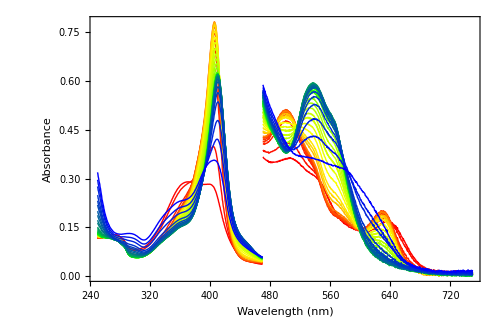

```mathematica
(*Check 470 nm...*)
break=1+Position[wavelength,Nearest[wavelength,471][[1]]][[1]][[1]];

hiw=wavelength[[1;;break]];
low=wavelength[[break+1;;height-1]];

traces={};
For[i=1,i≤Length[pHvals],i++,
AppendTo[traces,Transpose[{hiw,10*abs[[i]][[1;;break]]}]];
AppendTo[traces,Transpose[{low,abs[[i]][[break+1;;height-1]]}]]]

m=Last[pHvals];
d=m-pHvals[[1]];
colors={};
For[i=1,i≤Length[pHvals],i++,
AppendTo[colors,Directive[Blend[{Blue,Green,Yellow,Red},(m-pHvals[[i]])/d],Thickness[0.002]]];
AppendTo[colors,Directive[Blend[{Blue,Green,Yellow,Red},(m-pHvals[[i]])/d],Thickness[0.002]]]]

overlay=ListLinePlot[traces,
FrameLabel-> {"Wavelength (nm)","Absorbance"},
PlotRange->{{250,750},{0,All}},
PlotStyle->colors,
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->500
]
outfile="F:\\190524_K49A_THB1_Fe3_pH_titration/spectra_overlay.jpg";
Export[outfile,overlay,"EmbeddedFonts"->False];
```

### Pretty pH values...

3.41

12.66

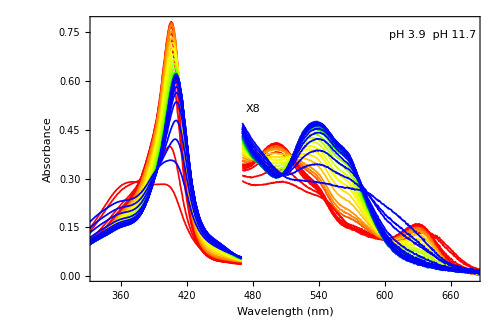

```mathematica
first=1; (*a que pH empieza, es el numero de la columna en los datos*)
last=-1; (*a que pH termina*)
pHvals[[first]]
pHvals[[last]]
trpHvals=pHvals[[first;;last]];
trabs=abs[[first;;last]];

trtraces={};
For[i=1,i≤Length[trpHvals],i++,
AppendTo[trtraces,Transpose[{hiw,8*trabs[[i]][[1;;break]]}]];
AppendTo[trtraces,Transpose[{low,trabs[[i]][[break+1;;height-1]]}]]]

trd=11-5;
trcolors={};
For[i=1,i≤Length[trpHvals],i++,
AppendTo[trcolors,Directive[Blend[{Blue,Green,Yellow,Red},(11-trpHvals[[i]])/trd],Thickness[0.0025]]];
AppendTo[trcolors,Directive[Blend[{Blue,Green,Yellow,Red},(11-trpHvals[[i]])/trd],Thickness[0.0025]]]]

troverlay=ListLinePlot[trtraces,
FrameLabel-> {"Wavelength (nm)","Absorbance"},
PlotRange->{{338.75,680},{0,All}},
PlotStyle->trcolors,
Epilog->{Inset["pH 3.9  pH 11.7",Scaled[{.99,.93}],Right,BaseStyle->{FontFamily->"Arial", FontSize->16}],
Inset["X8",Scaled[{.4,.65}],Left,BaseStyle->{FontFamily->"Arial", FontSize->16}]},
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->500
]
troutfile="F:\\190524_K49A_THB1_Fe3_pH_titration/spectra_overlay_pretty.jpg";
Export[troutfile,troverlay,"EmbeddedFonts"->False];
```

## Acid-Neutral-Basic Overlay

{4.92}

{8.48}

{10.75}

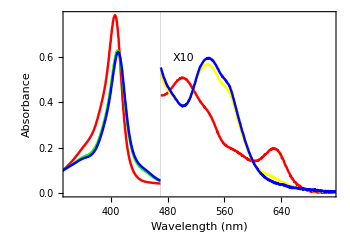

```mathematica
trpH={5,8.4,10.92};

traces={};
For[i=1,i≤Length[trpH],i++,
l=Position[pHvals,Nearest[pHvals,trpH[[i]]][[1]]][[1]][[1]];
Print[Nearest[pHvals,trpH[[i]]]];
AppendTo[traces,Transpose[{hiw,10*abs[[l]][[1;;break]]}]];
AppendTo[traces,Transpose[{low,abs[[l]][[break+1;;height-1]]}]]]

anb=ListLinePlot[traces,
FrameLabel-> {"Wavelength (nm)","Absorbance"},
PlotRange->{{340,710},{0,All}},
PlotStyle->{{Red,Thickness->0.005},{Red,Thickness->0.005},{Yellow,Thickness->0.005},{Green,Thickness->0.005},{Blue,Thickness->0.005},{Blue,Thickness->0.005}},
GridLines->{{470},None},
Epilog->{Inset["X10",Scaled[{.4,.75}],Left,BaseStyle->{FontFamily->"Arial", FontSize->20}]},
FrameTicks->{{Automatic,None},{Automatic,None}}]

(*outfile2="~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/spectra_overlay_abn.pdf";
Export[outfile2,anb,"EmbeddedFonts"->False];*)
```

## Single-Wavelength Abs vs. pH

### Any Wavelength

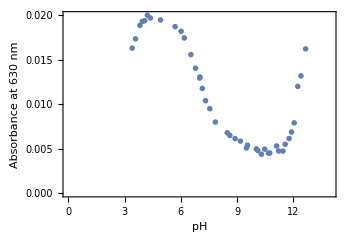

```mathematica
(*Change*)lambda=630;(*Change*)
pos=Position[wavelength,Nearest[wavelength,lambda][[1]]][[1]][[1]];
any=ListPlot[Transpose[{trpHvals,Transpose[trabs][[pos,All]]}],
FrameLabel-> {"pH","Absorbance at "<>ToString[lambda]<>" nm"},
PlotRange->{{0,14},{0.00,All}},
FrameTicks->{{Automatic,None},{Automatic,None}}]
```

### 407 nm + FIT

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

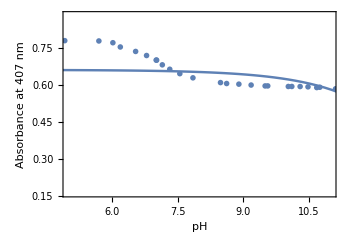

| Estimate | Standard Error | t-Statistic | P-Value
pKa | 21.8111 | 3080.77 | 0.00707975 | 0.994389
n | 0.321208 | 0.491867 | 0.653039 | 0.517768
a | -235.53 | 533791. | -0.000441241 | 0.99965
b | 0.660129 | 0.0277638 | 23.7766 | 5.16141×10^-24

```mathematica
pos=Position[wavelength,Nearest[wavelength,407][[1]]][[1]][[1]];
qdata=Transpose[{pHvals[[first;;last]],Transpose[abs][[pos,first;;last]]}];
a407=ListPlot[qdata,
FrameLabel-> {"pH","Absorbance at 407 nm"},
PlotRange->{{5,11},MinMax[qdata[[All,2]],Scaled[0.2]]},
FrameTicks->{{Automatic,None},{Automatic,None}}];
model=b+(a/(1+10^(n(pKa-pH))));
nlm407=NonlinearModelFit[qdata,model,{{pKa,8.5},{n,1},{a,-40},{b,150}},pH];
a407fit=Show[a407,
Plot[nlm407[pH],{pH,4,12},PlotStyle->{Thickness[0.005]}]]
nlm407["ParameterTable"]
(*Export["~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/a407.pdf",a407,"EmbeddedFonts"->False];
Export["~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/a407fit.pdf",a407fit,"EmbeddedFonts"->False];*)
```

### 450 nm + FIT

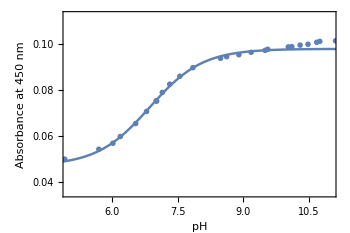

| Estimate | Standard Error | t-Statistic | P-Value
pKa | 6.8626 | 0.0695727 | 98.6393 | 2.07529×10^-46
n | 0.722253 | 0.0872468 | 8.27827 | 6.05508×10^-10
a | 0.0507009 | 0.0015283 | 33.1747 | 3.96208×10^-29
b | 0.0471379 | 0.00125346 | 37.6061 | 4.36398×10^-31

```mathematica
pos=Position[wavelength,Nearest[wavelength,450][[1]]][[1]][[1]];
qdata=Transpose[{pHvals[[first;;last]],Transpose[abs][[pos,first;;last]]}];
a450=ListPlot[qdata,
FrameLabel-> {"pH","Absorbance at 450 nm"},
PlotRange->{{5,11},MinMax[qdata[[All,2]],Scaled[0.2]]},
FrameTicks->{{Automatic,None},{Automatic,None}}];
model=b+(a/(1+10^(n(pKa-pH))));
nlm450=NonlinearModelFit[qdata,model,{{pKa,8.5},{n,1},{a,10},{b,10}},pH];
a450fit=Show[a450,
Plot[nlm450[pH],{pH,4,12},PlotStyle->{Thickness[0.005]}]]
nlm450["ParameterTable"]
(*Export["~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/a450.pdf",a450,"EmbeddedFonts"->False];
Export["~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/a450fit.pdf",a450fit,"EmbeddedFonts"->False];*)
```

### 570 nm + FIT

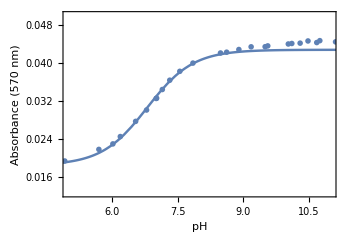

| Estimate | Standard Error | t-Statistic | P-Value
pKa | 6.80634 | 0.0868882 | 78.3345 | 1.00767×10^-42
n | 0.832266 | 0.138807 | 5.99584 | 6.36059×10^-7
a | 0.0242888 | 0.00095832 | 25.3452 | 5.54759×10^-25
b | 0.0185512 | 0.000795797 | 23.3115 | 1.02539×10^-23

```mathematica
pos=Position[wavelength,Nearest[wavelength,570][[1]]][[1]][[1]];
qdata=Transpose[{pHvals[[first;;last]],Transpose[abs][[pos,first;;last]]}];
a570=ListPlot[qdata,
FrameLabel-> {"pH","Absorbance (570 nm)"},
PlotRange->{{5,11},MinMax[qdata[[All,2]],Scaled[0.2]]},
FrameTicks->{{Automatic,None},{Automatic,None}}];
model=b+(a/(1+10^(n(pKa-pH))));
nlm570=NonlinearModelFit[qdata,model,{{pKa,8.5},{n,1},{a,6},{b,3}},pH];
a570fit=Show[a570,
Plot[nlm570[pH],{pH,4,12},PlotStyle->{Thickness[0.005]}]]
nlm570["ParameterTable"]
(*Export["~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/a570.pdf",a570,"EmbeddedFonts"->False];
Export["~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/a570fit.pdf",a570fit,"EmbeddedFonts"->False];*)
```

### 630 nm + FIT

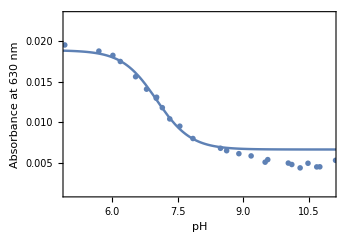

| Estimate | Standard Error | t-Statistic | P-Value
pKa | 7.01818 | 0.151524 | 46.3172 | 2.29247×10^-34
n | 1.10556 | 0.454674 | 2.43155 | 0.0199953
a | -0.0121868 | 0.00100235 | -12.1582 | 1.72768×10^-14
b | 0.0188429 | 0.000823271 | 22.8879 | 1.93606×10^-23

```mathematica
pos=Position[wavelength,Nearest[wavelength,630][[1]]][[1]][[1]];
qdata=Transpose[{pHvals[[first;;last]],Transpose[abs][[pos,first;;last]]}];
a630=ListPlot[qdata,
FrameLabel-> {"pH","Absorbance at 630 nm"},
PlotRange->{{5,11},MinMax[qdata[[All,2]],Scaled[0.2]]},
FrameTicks->{{Automatic,None},{Automatic,None}}];
model=b+(a/(1+10^(n(pKa-pH))));
nlm630=NonlinearModelFit[qdata,model,{{pKa,8.5},{n,1},{a,-3},{b,4}},pH];
a630fit=Show[a630,
Plot[nlm630[pH],{pH,4,12},PlotStyle->{Thickness[0.005]}]]
nlm630["ParameterTable"]
(*Export["~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/a630.pdf",a630,"EmbeddedFonts"->False];
Export["~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/a630fit.pdf",a630fit,"EmbeddedFonts"->False];*)
```

## Low-Spin SVD (430-700 nm, 5 < pH < 11)

```mathematica
hi=101;
lo=641;
wavelength[[hi]]
wavelength[[lo]]
trdata=Transpose[abs[[first;;last]]][[hi;;lo]];
{u,s,v}=SingularValueDecomposition[trdata];
Print["Roots of Eigenvalues"]
SingularValueList[trdata,5]
Print["Log of Eigenvalues"]
Log[SingularValueList[trdata,5]]
Print["Percentages of Eigenvalues"]
(100*(Diagonal[s]^2)/(Total[Diagonal[s]^2]))[[1;;5]]

st=s[[1;;5,1;;5]];
ut=u[[All,1;;5]];
vt=v[[All,1;;5]];
```

700.003

429.978

Roots of Eigenvalues

{6.87628,0.780822,0.224563,0.0747338,0.0254912}

Log of Eigenvalues

{1.92808,-0.247408,-1.4936,-2.59382,-3.66942}

Percentages of Eigenvalues

{98.6091,1.27149,0.105169,0.0116478,0.00135516}

### SV#1

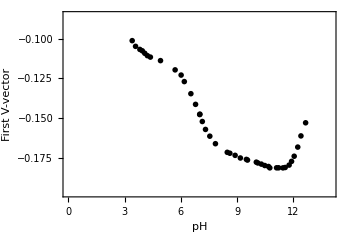

```mathematica
vtplot1=ListPlot[Transpose[{pHvals[[first;;last]],vt[[All,1]]}],FrameLabel-> {"pH","First V-vector"},
PlotRange->{{0,14},MinMax[vt[[All,1]],Scaled[0.2]]},
PlotStyle->Black]
```

### SV#2

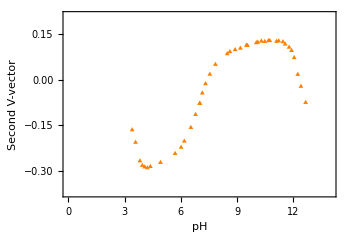

```mathematica
vtplot2=ListPlot[Transpose[{pHvals[[first;;last]],vt[[All,2]]}],FrameLabel-> {"pH","Second V-vector"},
PlotRange->{{0,14},MinMax[vt[[All,2]],Scaled[0.2]]},
PlotStyle->Orange,
PlotMarkers->{▲,17}]
```

### SV-Indexed Format & Global Fit (430-700 nm)

| Estimate | Standard Error | t-Statistic | P-Value
a1 | -0.111267 | 0.00923685 | -12.046 | 2.65947×10^-19
b1 | -0.175856 | 0.0063986 | -27.4835 | 3.15959×10^-41
a2 | -0.258154 | 0.0110199 | -23.4262 | 1.66191×10^-36
b2 | 0.0935982 | 0.00693654 | 13.4935 | 7.21354×10^-22
n | 1.00282 | 0.178466 | 5.61911 | 3.01819×10^-7
pka | 6.96864 | 0.0736346 | 94.638 | 1.2953×10^-80

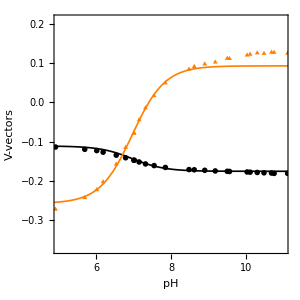

```mathematica
(*SV-indexed form of data*)
data1=Transpose[{pHvals[[first;;last]],vt[[All,1]]}];
data2=Transpose[{pHvals[[first;;last]],vt[[All,2]]}];
idata = Join[{1, Sequence @@ #} & /@ data1, {2, Sequence @@ #} & /@ data2];
(*Functions*)
f1[pH_]:=(a1*10^(n(pka-pH))+b1)/(10^(n(pka-pH))+1);
f2[pH_]:=(a2*10^(n(pka-pH))+b2)/(10^(n(pka-pH))+1);
imodel[i_,pH_]:=KroneckerDelta[i-1]*f1[pH]+KroneckerDelta[i-2]*f2[pH];
a1=.
b1=.
a2=.
b2=.
n=.
pka=.
inlm=NonlinearModelFit[idata,imodel[index,x],
{{a1,-0.16},{b1,-1},
{a2,-0.25},{b2,1},
{n,1},{pka,8.5}},{index,x}];
inlm["ParameterTable"]
ifit1=Show[vtplot1,
Plot[inlm[1,pH],{pH,0,14},PlotStyle->{Black,Thickness[0.004]}]];
ifit2=Show[vtplot2,
Plot[inlm[2,pH],{pH,0,14},PlotStyle->{Orange,Thickness[0.004]}]];
sv=Show[{ifit1,ifit2},
PlotRange->{{5,11},MinMax[vt[[All,1;;2]],Scaled[0.2]]},
FrameLabel-> {"pH","V-vectors"},
(*Epilog->{Inset[Style["● V_1(pH)",Black],Scaled[{0.05,0.9}],Left,BaseStyle->{FontFamily->"Arial",FontWeight-> Bold, FontSize->20}],
Inset[Style["▲ V_2(pH)",Blue],Scaled[{0.05,0.8}],Left,BaseStyle->{FontFamily->"Arial",FontWeight-> Bold, FontSize->20}],
Inset[Style["pK_app ="<>ToString[PaddedForm[inlm["BestFitParameters"][[6,2]],{3,2}]]<>" ±"<>ToString[PaddedForm[inlm["ParameterErrors"][[6]],{1,2}]],Black],Scaled[{0.05,0.7}],Left,BaseStyle->{FontFamily->"Arial", FontSize->20}],Inset[Style["n ="<>ToString[PaddedForm[inlm["BestFitParameters"][[5,2]],{3,2}]]<>" ±"<>ToString[PaddedForm[inlm["ParameterErrors"][[5]],{1,2}]],Black],Scaled[{0.05,0.6}],Left,BaseStyle->{FontFamily->"Arial", FontSize->20}]},*)
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->300,
AspectRatio->1
]
(*svoutfile="~/odrive/Box/Lecomte_Lab/pH_Titrations/K49E_THB1_Fe3_pH_titration_2/svd.pdf";
Export[svoutfile,sv,"EmbeddedFonts"->False];*)
```

### Population plot

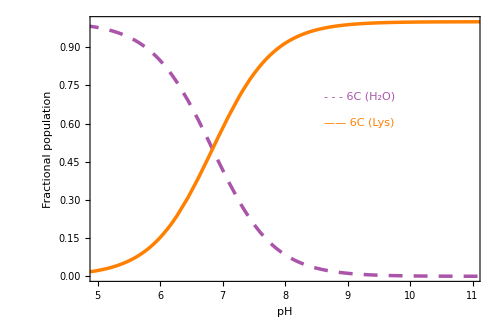

```mathematica
pop[b_,a_,n1_,pka1_,pH_]:=b+a/(1+10^(n1(pka1-pH)));
Plot[{pop[1,-1,0.89,6.84,pH],
pop[0,1,0.89,6.84,pH]},{pH,4,12},
Axes->False,
AspectRatio->2/3,
BaseStyle->{FontFamily->"Arial",
FontSize->20,
FontWeight->Normal},
Frame-> True,
ImageSize->500,
FrameStyle-> AbsoluteThickness[1],
LabelStyle-> Directive[Black],
PlotRange->{{5,11},{0,1}},
FrameLabel->{"pH","Fractional population"},
FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->{{AbsoluteDashing[{10,8}],Lighter[Purple],Thickness[0.005]},
{Orange,Thickness[0.005]}},
Epilog->{Inset[Style["- - - 6C (H_2O)",Lighter[Purple]],Scaled[{0.6,0.7}],Left,BaseStyle->{FontFamily->"Arial",FontWeight-> Bold, FontSize->20}],
Inset[Style["—— 6C (Lys)",Orange],Scaled[{0.6,0.6}],Left,BaseStyle->{FontFamily->"Arial",FontWeight-> Bold, FontSize->20}]}]
```